# (n=1) lensing bands in Kerr spacetime (benchmark)

This notebook demonstrates (some of) the current capabilities of LBeyondGR, using the example of Kerr spacetime.
The notebook can be evaluated from top to bottom (without prior execution of initialization cells).
Alternatively, the user may evaluate the initialization cells and then evaluate individual subsections below.

Note that only initialization cells will be executed when exported and executed as a .m file.
(This might be important when running .m files automatically on a cluster.)

## setup

This section contains the initialization cells necessary for the remainder of the notebook.

### initialization

Set some plotting presets.

```mathematica
texStyle = {FontFamily -> "Latin Modern Roman", FontSize -> 16, FontColor->Black};
```

Load the package (not an initialization cell: if the notebook is called this will be done externally) ...

```mathematica
If[! TrueQ[$FrontEnd == Null], SetDirectory[NotebookDirectory[]]]
Import["../../pkg/LBeyondGR.m"];
```

/home/aaron/GITs/current/LBeyondGR/examples/Kerr

========================================================================
LBeyondGR package is being loaded.
 =============================
version: last updated 26-Oct-2023
=======================================================================

Set the asymptotic parameters and Newton coupling (required for transformation from oblate spheroidal to screen coordinates).

```mathematica
SetMass[M];
SetNewtonCoupling[1];
SetSpin[α];
{$mass,$spin,$G0};
```

Set the BL-coordinates coordinates.

```mathematica
SetBoyerLindquistCoords[t,r,θ,χ];
GetBoyerLindquistCoords[];
WhichCoords;
```

At the moment, the metric and connection (Christoffel symbols) need to be specified separately.
These can, for instance, be derived using xAct, cf. initKerr.nb.
Here, we import the resulting .m file and set the metric and christoffels.

```mathematica
Import["initSpacetime.m"]
```

You can, for instance, have a look at the specified metric. It is important that the coordinates are the same as specified above (and that the asymptotic parameters match those specified as mass and spin).

```mathematica
metric//TableForm
```

-1+(2 M r)/(r^2+α^2 Cos[θ]^2) | 0 | 0 | -(2 M r α Sin[θ]^2)/(r^2+α^2 Cos[θ]^2)
0 | (r^2+α^2 Cos[θ]^2)/(-2 M r+r^2+α^2) | 0 | 0
0 | 0 | r^2+α^2 Cos[θ]^2 | 0
-(2 M r α Sin[θ]^2)/(r^2+α^2 Cos[θ]^2) | 0 | 0 | Sin[θ]^2 (r^2+α^2+(2 M r α^2 Sin[θ]^2)/(r^2+α^2 Cos[θ]^2))

```mathematica
SetMetric[gMetric, metric];
SetChristoffel[christoffelOf[gMetric],christoffel];
```

The metric can now be retrieved with GetMetric[], with an index-notation similar to xAct.

```mathematica
FullSimplify[Table[GetMetric[-ii,-jj],{ii,1,4},{jj,1,4}],Trig->True]//TableForm
```

-1+(2 M r)/(r^2+α^2 Cos[θ]^2) | 0 | 0 | -(2 M r α Sin[θ]^2)/(r^2+α^2 Cos[θ]^2)
0 | (r^2+α^2 Cos[θ]^2)/(-2 M r+r^2+α^2) | 0 | 0
0 | 0 | r^2+α^2 Cos[θ]^2 | 0
-(2 M r α Sin[θ]^2)/(r^2+α^2 Cos[θ]^2) | 0 | 0 | Sin[θ]^2 (r^2+α^2+(2 M r α^2 Sin[θ]^2)/(r^2+α^2 Cos[θ]^2))

### import previously obtained data

Here we import data potentially generated in previous runs.
(The filenames match the filenames in the code below. If these are altered by the user, they have to be altered consistently.)

```mathematica
SetDirectory[NotebookDirectory[]];
Import["dat/Kerr.m"];
```

Import::nffil: File dat/Kerr.m not found during Import.

### demonstrate internal single ray tracing

The Kerr metric which was initialized before has two free parameters: the mass M, and the spin parameter α.  In general, all such parameter values have to be passed as rules to all the numerical functions.

GetSingleLightRay[rCam_,θCam_,ϕCam_},{xScreen_,yScreen_},paramRules_List] 
is a function which to numerically integrate the geodesic equation of a single light ray in the presently set spacetime.
PlotSingleTrajectory[sol_, paramRules_List]
is a plot routine to plot the outcome of GetSingleLightRay[]. It takes the same options as Mathematica’s Plot3D routine. In addition the user can specify to plot the horizon or not.

```mathematica
?GetSingleLightRay
?PlotSingleTrajectory
```

You can explore single light rays by varying the screen coordinates below

```mathematica
screenX = Rationalize[0,1*^-100];
screenY = Rationalize[4.92,1*^-100];
params = {M->1,α->99/100};

sol = GetSingleLightRay[{100,π,π/3},{screenX,screenY},params,WorkingPrecision->20][[1]];
Quiet@PlotSingleTrajectory[sol, params, PlotRange->{{-10,10},{-10,10},{-10,10}}]
```

trajectory escapes: at λ=217.54 the radial coordinate has surpassed the radial camera distance

-Graphics3D-

As a test of the internal numerics (which uses Mathematica’s NDSolve), you can check the constants of motion along the trajectory.

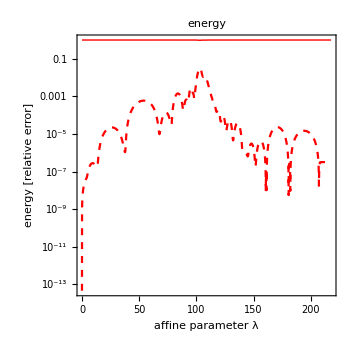

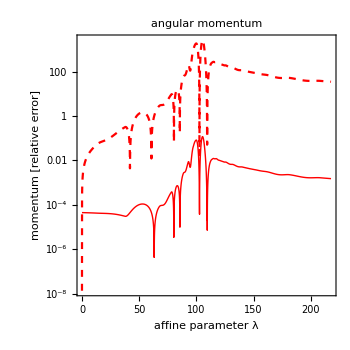

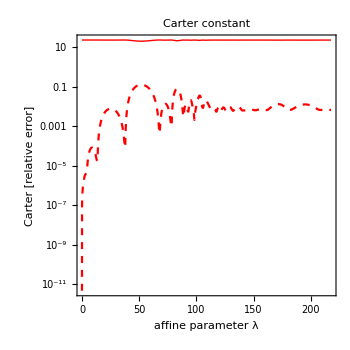

maximalErrors | 0.0316127 | 2647.73 | 0.12715
finalTimeErrors | 3.2448668247×10^-7 | 34.906053567041527 | 0.006713916210959462

```mathematica
CheckConstantsOfMotionAlongRay[sol,{M->1,α->9/10},α]//TableForm
```

## obtain lensing-band bisections

We perform some benchmark tests, comparing to images obtained with AART (https://github.com/iAART/aart).

### benchmark: lensing-band (spin=94/100, incl=(17π)/180)

#### setup

Here, we fix the camera (to M87*-angle) and the two sets of spacetime-geometry parameters.
The ϕ angle (third entry) is irrelevant.

```mathematica
camera = {1000,17π/180,π/5};
```

```mathematica
paramsGR = {
	G0->1,M->1,α->-94/100,δHor->1*^-2
};
```

#### get data for lensing band

Inner shadow

```mathematica
First@Timing[
	LBinner[0][camera, paramsGR] = Quiet@GetLensingBand[
		camera,
		{{0,0}, {10,3}},
		paramsGR,
		(*horizon*)
		HorizonCondition -> (($r < M + Sqrt[M^2 - α^2] + δHor)/.paramsGR),
		(*precision and step size*)
		PrecisionGoalForBisection->10^-2,
		InitialStepSize->5*10^-1,
		(*NDSolve options*)
		PrecisionGoal->4, 
		(*do NOT use WorkingPrecision or AccuracyGoal since this seems to significantly slow down / worsen the numerics*)
		MaxSteps->10^4,
		(*lensing band specification*)
		WhichLensingBand->inner, WhichLensingBandNumber->0,
		UseShadowBoundaryForEntryPoint->True, 
		(*stop conditions*)
		MaxNumberOfSteps->∞, OutOfBoundsValue->20,
		(*progress plot and prints*)
		ShowProgressPlot->True, PlotRange->{{-10,10},{-10,10}}, PrintTemporaryOption->False
	];
]
```

21.3401

Inner n=1 lensing band

```mathematica
First@Timing[
	LBinner[1][camera, paramsGR] = Quiet@GetLensingBand[
		camera,
		{{0,0}, {10,3}},
		paramsGR,
		(*horizon*)
		HorizonCondition -> (($r < M + Sqrt[M^2 - α^2] + δHor)/.paramsGR),
		(*precision and step size*)
		PrecisionGoalForBisection->10^-2,
		InitialStepSize->5*10^-1,
		(*NDSolve options*)
		PrecisionGoal->10,(*do NOT use AccuracyGoal since this seems to significantly slow down the numerics*)
		MaxSteps->10^4,
		(*lensing band specification*)
		WhichLensingBand->inner, WhichLensingBandNumber->1,
		UseShadowBoundaryForEntryPoint->True, 
		(*stop conditions*)
		MaxNumberOfSteps->∞, OutOfBoundsValue->20,
		(*progress plot and prints*)
		ShowProgressPlot->True, PlotRange->{{-10,10},{-10,10}}, PrintTemporaryOption->False
	];
]
```

37.5336

Outer n=1 lensing band

```mathematica
First@Timing[
	LBouter[1][camera, paramsGR] = Quiet@GetLensingBand[
		camera,
		{{0,0}, {10,3}},
		paramsGR,
		(*horizon*)
		HorizonCondition -> (($r < M + Sqrt[M^2 - α^2] + δHor)/.paramsGR),
		(*precision and step size*)
		PrecisionGoalForBisection->10^-2,
		InitialStepSize->5*10^-1,
		(*NDSolve options*)
		PrecisionGoal->10,(*do NOT use AccuracyGoal since this seems to significantly slow down the numerics*)
		MaxSteps->10^4,
		(*lensing band specification*)
		WhichLensingBand->outer, WhichLensingBandNumber->1,
		UseShadowBoundaryForEntryPoint->True, 
		(*stop conditions*)
		MaxNumberOfSteps->∞, OutOfBoundsValue->20,
		(*progress plot and prints*)
		ShowProgressPlot->True, PlotRange->{{-10,10},{-10,10}}, PrintTemporaryOption->False
	];
]
```

56.0297

```mathematica
SetDirectory[NotebookDirectory[]];
DumpSave[
	"dat/Kerr.m",
	{
		LBinner, LBouter
	}
];
```

#### plot lensing band

```mathematica
SetDirectory[NotebookDirectory[]];
Import["dat/Kerr.m"];

LB0GR = Graphics[
	{
		EdgeForm[{Thin,Gray}],
		Opacity[0.7,Black],
		FilledCurve[{
				{Line[LBinner[0][camera,#]]}
			}]&@paramsGR
	}
];

LB1GR = Graphics[
	{
		EdgeForm[{Thin,Gray}],
		Opacity[0.3,Darker@RGBColor["#0070ff"]],
		FilledCurve[{
				{Line[LBinner[1][camera,#]]},
				{Line[LBouter[1][camera,#]]}
			}]&@paramsGR
	}
];
```

```mathematica
SetDirectory[NotebookDirectory[]];
n1innerAlejo=Import["dat/benchmark_Alejandro/LensingInfo_a0.94_i17.txt","Data"][[All,3;;4]];
n1outerAlejo=Import["dat/benchmark_Alejandro/LensingInfo_a0.94_i17.txt","Data"][[All,5;;6]];

LB1GRinnerAlejo = Line[n1innerAlejo];
LB1GRouterAlejo = Line[n1outerAlejo];
LB1GRAlejo = Graphics[
	{
		Opacity[0.3,RGBColor["#ff8f00"]],
		FilledCurve[{{LB1GRinnerAlejo},{LB1GRouterAlejo}}]
	}
];
```

```mathematica
range = 8;

plotFrameLeft = ListPlot[
	{},
	BaseStyle -> texStyle,
	PlotRange -> {{-range,range},{-range,range}},
	FrameLabel->None(*{
		MaTeX["x_\\text{im}\;\;[M]"],
		MaTeX["y_\\text{im}\;\;[M]"]
	}*),
	LabelStyle->{16,Black},
	ImageSize->300,AspectRatio->1,
	GridLines->{Table[ii,{ii,-100,100,5}],Table[ii,{ii,-100,100,5}]}, 
	GridLinesStyle->Directive[Thin,Lighter@Lighter@Lighter@Lighter@Gray],
	Frame->True, Axes->False, FrameStyle->Directive[Black],
	FrameTicks->{{Table[ii,{ii,-100,100,5}],None},{Table[ii,{ii,-100,100,5}],None}}, FrameTicksStyle->Directive[Black,12]
];

plotFrameRight = ListPlot[
	{},
	BaseStyle -> texStyle,
	PlotRange -> {{-range,range},{-range,range}},
	FrameLabel->None(*{
		MaTeX["x_\\text{im}\;\;[M]"],
		MaTeX["y_\\text{im}\;\;[M]"]
	}*),
	LabelStyle->{16,Black},
	ImageSize->300,AspectRatio->1,
	GridLines->{Table[ii,{ii,-100,100,5}],Table[ii,{ii,-100,100,5}]}, 
	GridLinesStyle->Directive[Thin,Lighter@Lighter@Lighter@Lighter@Gray],
	Frame->True, Axes->False, FrameStyle->Directive[Black],
	FrameTicks->{{None,Table[ii,{ii,-100,100,5}]},{Table[ii,{ii,-100,100,5}],None}}, FrameTicksStyle->Directive[Black,12]
];
```

```mathematica
plot[paramsGR] = Show[
	plotFrameLeft, LB0GR, LB1GR, LB1GRAlejo,
	Epilog->{
			Inset[Rotate[MaTeX["a/M=0.94"],0],{-range,range}*0.9,{Left,Top}],
			Inset[Rotate[MaTeX["\\theta_\\text{obs}=17\\pi/180"],0],{range,range}*0.9,{Right,Top}],
			Inset[Rotate[MaTeX["\\longrightarrow x"],0],{-range,-range}*0.95,{Left,Bottom}],
			Inset[Rotate[MaTeX["\\longrightarrow \\rotatebox[origin=c]{-90}{y}"],π/2],{-range,-range}*0.95,{Left,Bottom}]
		}
]

SetDirectory[NotebookDirectory[]];
Export["plots/benchmark-Kerr_incl{17pi;180}_spin{94;100}.pdf",plot[paramsGR]]
```

-Graphics-

plots/benchmark-Kerr_incl{17pi;180}_spin{94;100}.pdf

### benchmark: lensing-band (spin=5/10, incl=(45π)/180)

#### setup

Here, we fix the camera (to M87*-angle) and the two sets of spacetime-geometry parameters.

```mathematica
camera = {1000,45π/180,π/5};
```

```mathematica
paramsGR = {
	G0->1,M->1,α->-5/10,δHor->1*^-2
};
```

#### get data for lensing band

```mathematica
First@Timing[
	LBinner[0][camera, paramsGR] = Quiet@GetLensingBand[
		camera,
		{{0,0}, {10,3}},
		paramsGR,
		(*horizon*)
		HorizonCondition -> (($r < M + Sqrt[M^2 - α^2] + δHor)/.paramsGR),
		(*precision and step size*)
		PrecisionGoalForBisection->10^-2,
		InitialStepSize->5*10^-1,
		(*NDSolve options*)
		PrecisionGoal->10,(*do NOT use AccuracyGoal since this seems to significantly slow down the numerics*)
		MaxSteps->10^4,
		(*lensing band specification*)
		WhichLensingBand->inner, WhichLensingBandNumber->0,
		UseShadowBoundaryForEntryPoint->True, 
		(*stop conditions*)
		MaxNumberOfSteps->∞, OutOfBoundsValue->20,
		(*progress plot and prints*)
		ShowProgressPlot->True, PlotRange->{{-10,10},{-10,10}}, PrintTemporaryOption->False
	];
]
```

30.8129

```mathematica
First@Timing[
	LBinner[1][camera, paramsGR] = Quiet@GetLensingBand[
		camera,
		{{0,0}, {10,3}},
		paramsGR,
		(*horizon*)
		HorizonCondition -> (($r < M + Sqrt[M^2 - α^2] + δHor)/.paramsGR),
		(*precision and step size*)
		PrecisionGoalForBisection->10^-2,
		InitialStepSize->5*10^-1,
		(*NDSolve options*)
		PrecisionGoal->10,(*do NOT use AccuracyGoal since this seems to significantly slow down the numerics*)
		MaxSteps->10^4,
		(*lensing band specification*)
		WhichLensingBand->inner, WhichLensingBandNumber->1,
		UseShadowBoundaryForEntryPoint->True, 
		(*stop conditions*)
		MaxNumberOfSteps->∞, OutOfBoundsValue->20,
		(*progress plot and prints*)
		ShowProgressPlot->True, PlotRange->{{-10,10},{-10,10}}, PrintTemporaryOption->False
	];
]
```

48.6402

```mathematica
First@Timing[
	LBouter[1][camera, paramsGR] = Quiet@GetLensingBand[
		camera,
		{{0,0}, {10,3}},
		paramsGR,
		(*horizon*)
		HorizonCondition -> (($r < M + Sqrt[M^2 - α^2] + δHor)/.paramsGR),
		(*precision and step size*)
		PrecisionGoalForBisection->10^-2,
		InitialStepSize->5*10^-1,
		(*NDSolve options*)
		PrecisionGoal->10,(*do NOT use AccuracyGoal since this seems to significantly slow down the numerics*)
		MaxSteps->10^4,
		(*lensing band specification*)
		WhichLensingBand->outer, WhichLensingBandNumber->1,
		UseShadowBoundaryForEntryPoint->True, 
		(*stop conditions*)
		MaxNumberOfSteps->∞, OutOfBoundsValue->20,
		(*progress plot and prints*)
		ShowProgressPlot->True, PlotRange->{{-10,10},{-10,10}}, PrintTemporaryOption->False
	];
]
```

67.6165

```mathematica
SetDirectory[NotebookDirectory[]];
DumpSave[
	"dat/Kerr.m",
	{
		LBinner, LBouter
	}
];
```

#### plot lensing band

```mathematica
SetDirectory[NotebookDirectory[]];
Import["dat/Kerr.m"];

LB0GR = Graphics[
	{
		EdgeForm[{Thin,Gray}],
		Opacity[0.7,Black],
		FilledCurve[{
				{Line[LBinner[0][camera,#]]}
			}]&@paramsGR
	}
];

LB1GR = Graphics[
	{
		EdgeForm[{Thin,Gray}],
		Opacity[0.3,Darker@RGBColor["#0070ff"]],
		FilledCurve[{
				{Line[LBinner[1][camera,#]]},
				{Line[LBouter[1][camera,#]]}
			}]&@paramsGR
	}
];
```

```mathematica
SetDirectory[NotebookDirectory[]];
n1innerAlejo=Import["dat/benchmark_Alejandro/LensingInfo_a0.5_i45.txt","Data"][[All,3;;4]];
n1outerAlejo=Import["dat/benchmark_Alejandro/LensingInfo_a0.5_i45.txt","Data"][[All,5;;6]];

LB1GRinnerAlejo = Line[n1innerAlejo];
LB1GRouterAlejo = Line[n1outerAlejo];
LB1GRAlejo = Graphics[
	{
		Opacity[0.3,RGBColor["#ff8f00"]],
		FilledCurve[{{LB1GRinnerAlejo},{LB1GRouterAlejo}}]
	}
];
```

```mathematica
range = 11;

plotFrameLeft = ListPlot[
	{},
	BaseStyle -> texStyle,
	PlotRange -> {{-range,range},{-range,range}},
	FrameLabel->None(*{
		MaTeX["x_\\text{im}\;\;[M]"],
		MaTeX["y_\\text{im}\;\;[M]"]
	}*),
	LabelStyle->{16,Black},
	ImageSize->300,AspectRatio->1,
	GridLines->{Table[ii,{ii,-100,100,5}],Table[ii,{ii,-100,100,5}]}, 
	GridLinesStyle->Directive[Thin,Lighter@Lighter@Lighter@Lighter@Gray],
	Frame->True, Axes->False, FrameStyle->Directive[Black],
	FrameTicks->{{Table[ii,{ii,-100,100,5}],None},{Table[ii,{ii,-100,100,5}],None}}, FrameTicksStyle->Directive[Black,12]
];

plotFrameRight = ListPlot[
	{},
	BaseStyle -> texStyle,
	PlotRange -> {{-range,range},{-range,range}},
	FrameLabel->None(*{
		MaTeX["x_\\text{im}\;\;[M]"],
		MaTeX["y_\\text{im}\;\;[M]"]
	}*),
	LabelStyle->{16,Black},
	ImageSize->300,AspectRatio->1,
	GridLines->{Table[ii,{ii,-100,100,5}],Table[ii,{ii,-100,100,5}]}, 
	GridLinesStyle->Directive[Thin,Lighter@Lighter@Lighter@Lighter@Gray],
	Frame->True, Axes->False, FrameStyle->Directive[Black],
	FrameTicks->{{None,Table[ii,{ii,-100,100,5}]},{Table[ii,{ii,-100,100,5}],None}}, FrameTicksStyle->Directive[Black,12]
];
```

```mathematica
plot[paramsGR] = Show[
	plotFrameLeft, LB0GR, LB1GR, LB1GRAlejo,
	Epilog->{
			Inset[Rotate[MaTeX["a/M=0.94"],0],{-range,range}*0.9,{Left,Top}],
			Inset[Rotate[MaTeX["\\theta_\\text{obs}=45\\pi/180"],0],{range,range}*0.9,{Right,Top}],
			Inset[Rotate[MaTeX["\\longrightarrow x"],0],{-range,-range}*0.95,{Left,Bottom}],
			Inset[Rotate[MaTeX["\\longrightarrow \\rotatebox[origin=c]{-90}{y}"],π/2],{-range,-range}*0.95,{Left,Bottom}]
		}
]

SetDirectory[NotebookDirectory[]];
Export["plots/benchmark-Kerr_incl{45pi;180}_spin{5;10}.pdf",plot[paramsGR]]
```

-Graphics-

plots/benchmark-Kerr_incl{45pi;180}_spin{5;10}.pdf

### benchmark: lensing-band (spin=99/100, incl=(85π)/180)

#### setup

Here, we fix the camera (to M87*-angle) and the two sets of spacetime-geometry parameters.

```mathematica
camera = {100000,85π/180,π/5};
```

```mathematica
paramsGR = {
	G0->1,M->1,α->-99/100,δHor->1*^-2
};
```

#### get data for lensing band

```mathematica
First@Timing[
	LBinner[0][camera, paramsGR] = Quiet@GetLensingBand[
		camera,
		{{0,0}, {10,10}},
		paramsGR,
		(*horizon*)
		HorizonCondition -> (($r < M + Sqrt[M^2 - α^2] + δHor)/.paramsGR),
		(*precision and step size*)
		PrecisionGoalForBisection->10^-2,
		InitialStepSize->1*10^-1,
		(*NDSolve options*)
		PrecisionGoal->10,(*do NOT use AccuracyGoal since this seems to significantly slow down the numerics*)
		MaxSteps->10^5,
		(*lensing band specification*)
		WhichLensingBand->inner, WhichLensingBandNumber->0,
		UseShadowBoundaryForEntryPoint->True, 
		(*stop conditions*)
		MaxNumberOfSteps->10^6, OutOfBoundsValue->100,
		(*progress plot and prints*)
		ShowProgressPlot->True, PlotRange->{{-10,10},{-10,10}}, PrintTemporaryOption->False
	];
]
```

33.3777

```mathematica
First@Timing[
	LBinner[1][camera, paramsGR] = Quiet@GetLensingBand[
		camera,
		{{0,0}, {10,10}},
		paramsGR,
		(*horizon*)
		HorizonCondition -> (($r < M + Sqrt[M^2 - α^2] + δHor)/.paramsGR),
		(*precision and step size*)
		PrecisionGoalForBisection->10^-2,
		InitialStepSize->1*10^-1,
		(*NDSolve options*)
		PrecisionGoal->10,(*do NOT use AccuracyGoal since this seems to significantly slow down the numerics*)
		MaxSteps->10^5,
		(*lensing band specification*)
		WhichLensingBand->inner, WhichLensingBandNumber->1,
		UseShadowBoundaryForEntryPoint->True, 
		(*stop conditions*)
		MaxNumberOfSteps->∞, OutOfBoundsValue->100,
		(*progress plot and prints*)
		ShowProgressPlot->True, PlotRange->{{-40,40},{-70,10}}, PrintTemporaryOption->False
	];
]
```

49.671

```mathematica
First@Timing[
	LBouter[1][camera, paramsGR] = Quiet@GetLensingBand[
		camera,
		{{0,0}, {10,10}},
		paramsGR,
		(*horizon*)
		HorizonCondition -> (($r < M + Sqrt[M^2 - α^2] + δHor)/.paramsGR),
		(*precision and step size*)
		PrecisionGoalForBisection->10^-2,
		InitialStepSize->5*10^-1,
		(*NDSolve options*)
		PrecisionGoal->10,(*do NOT use AccuracyGoal since this seems to significantly slow down the numerics*)
		MaxSteps->10^5,
		(*lensing band specification*)
		WhichLensingBand->outer, WhichLensingBandNumber->1,
		UseShadowBoundaryForEntryPoint->True, 
		(*stop conditions*)
		MaxNumberOfSteps->∞, OutOfBoundsValue->100,
		(*progress plot and prints*)
		ShowProgressPlot->True, PlotRange->{{-40,40},{-70,10}}, PrintTemporaryOption->False
	];
]
```

209.76

```mathematica
SetDirectory[NotebookDirectory[]];
DumpSave[
	"dat/Kerr.m",
	{
		LBinner, LBouter
	}
];
```

#### plot lensing band

```mathematica
SetDirectory[NotebookDirectory[]];
Import["dat/Kerr.m"];

LB0GR = Graphics[
	{
		EdgeForm[{Thin,Gray}],
		Opacity[0.7,Black],
		FilledCurve[{
				{Line[LBinner[0][camera,#]]}
			}]&@paramsGR
	}
];

LB1GR = Graphics[
	{
		EdgeForm[{Thin,Gray}],
		Opacity[0.3,Darker@RGBColor["#0070ff"]],
		FilledCurve[{
				{Line[LBinner[1][camera,#]]},
				{Line[LBouter[1][camera,#]]}
			}]&@paramsGR
	}
];
```

```mathematica
SetDirectory[NotebookDirectory[]];
n1innerAlejo=Import["dat/benchmark_Alejandro/LensingInfo_a0.99_i85.txt","Data"][[All,3;;4]];
n1outerAlejo=Import["dat/benchmark_Alejandro/LensingInfo_a0.99_i85.txt","Data"][[All,5;;6]];

LB1GRinnerAlejo = Line[n1innerAlejo];
LB1GRouterAlejo = Line[n1outerAlejo];
LB1GRAlejo = Graphics[
	{
		Opacity[0.3,RGBColor["#ff8f00"]],
		FilledCurve[{{LB1GRinnerAlejo},{LB1GRouterAlejo}}]
	}
];
```

```mathematica
range = 32;

plotFrameLeft = ListPlot[
	{},
	BaseStyle -> texStyle,
	PlotRange -> {{-range,range},{-52,12}},
	FrameLabel->None(*{
		MaTeX["x_\\text{im}\;\;[M]"],
		MaTeX["y_\\text{im}\;\;[M]"]
	}*),
	LabelStyle->{16,Black},
	ImageSize->300,AspectRatio->1,
	GridLines->{Table[ii,{ii,-100,100,20}],Table[ii,{ii,-100,100,20}]}, 
	GridLinesStyle->Directive[Thin,Lighter@Lighter@Lighter@Lighter@Gray],
	Frame->True, Axes->False, FrameStyle->Directive[Black],
	FrameTicks->{{Table[ii,{ii,-100,100,20}],None},{Table[ii,{ii,-100,100,20}],None}}, FrameTicksStyle->Directive[Black,12]
];

plotFrameRight = ListPlot[
	{},
	BaseStyle -> texStyle,
	PlotRange -> {{-range,range},{-range,range}},
	FrameLabel->None(*{
		MaTeX["x_\\text{im}\;\;[M]"],
		MaTeX["y_\\text{im}\;\;[M]"]
	}*),
	LabelStyle->{16,Black},
	ImageSize->200,AspectRatio->1,
	GridLines->{Table[ii,{ii,-100,100,20}],Table[ii,{ii,-100,100,20}]}, 
	GridLinesStyle->Directive[Thin,Lighter@Lighter@Lighter@Lighter@Gray],
	Frame->True, Axes->False, FrameStyle->Directive[Black],
	FrameTicks->{{None,Table[ii,{ii,-100,100,20}]},{Table[ii,{ii,-100,100,20}],None}}, FrameTicksStyle->Directive[Black,12]
];
```

```mathematica
plot[paramsGR] = Show[
	plotFrameLeft, LB0GR, LB1GR, LB1GRAlejo,
	Epilog->{
			Inset[Rotate[MaTeX["a/M=0.99"],0],{-range,range}*0.9-{0,20},{Left,Top}],
			Inset[Rotate[MaTeX["\\theta_\\text{obs}=85\\pi/180"],0],{range,range}*0.9-{0,20},{Right,Top}],
			Inset[Rotate[MaTeX["\\longrightarrow x"],0],{-range,-range}*0.95-{0,20},{Left,Bottom}],
			Inset[Rotate[MaTeX["\\longrightarrow \\rotatebox[origin=c]{-90}{y}"],π/2],{-range,-range}*0.95-{0,20},{Left,Bottom}]
		}
]

SetDirectory[NotebookDirectory[]];
Export["plots/benchmark-Kerr_incl{85pi;180}_spin{99;100}.pdf",plot[paramsGR]]
```

-Graphics-

plots/benchmark-Kerr_incl{85pi;180}_spin{99;100}.pdf

## minimize the overlap with an observed/assumed lensed emission region

### implement an observed/assumed lensed emission region

Here, we model an observed/assumed lensed emission region. 
See also [Broderick et.Al, The Astrophysical Journal 935, 61 (2022)].

```mathematica
μasToRad[β_]:=β*(2π)/(360*60*60) 10^-6;
```

```mathematica
GetThinM87RingInUnitsOfM9[LBRinμas_,fractionalWidth_,M9_] := Block[
	{
		GN = 6.6743*10^-11 m^3/(kg s^2),
		c = 299792458 m/s,
		Msun = 1.98847*10^30 kg,
		DM87 = (16.8)(3.086*10^22 m),
		M,θM,LBRinM9,outerThinRing,innerThinRing,thinRing
	},
	M = M9*10^9*Msun;
	θM = (GN*M)/(DM87 c^2);
	LBRinM9 = ArcTan[μasToRad[LBRinμas]]*1/θM;
	outerThinRing = DeleteDuplicates@Table[(1+fractionalWidth/2)LBRinM9*{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π,π/100}];
	innerThinRing = DeleteDuplicates@Table[(1-fractionalWidth/2)*LBRinM9*{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π,π/100}];

	thinRing = GetLBRegion[innerThinRing,outerThinRing];
	Return@thinRing
];
```

Other assumption may be implemented. The only technical requirement is that the user provides a “BoundaryMeshRegion”.

### random test GR

For each random instance, this section should be evaluated in its entirety

#### set camera

Here, we set up a camera/screen/telescope.
We leave “incl” to be specified later on.

```mathematica
camera = {10000,incl,π/5};
```

#### set random params

We generate some random choice of parameters.
(This amounts to an instance which may be implemented in an MCMC which can then explore the parameter space.)

We focus on high inclination since these are the more interesting cases

```mathematica
paramsGR = {
		G0->1,
		incl->Rationalize[(RandomReal[{60,85}]π)/180,10^-20],
		M9->Rationalize[RandomReal[{5,8}],10^-20],
		M->1, 
		α->Rationalize[RandomReal[{0,1}],10^-20], 
		δHor->1*^-2
	};

paramsGR//N//TableForm
incl*180/π/.paramsGR//N
```

G0→1.
incl→1.211
M9→7.82428
M→1.
α→0.611655
δHor→0.01

69.3854

#### set observed/assumed lensed emission region

We set an observed/assumed lensed emission region (modelled above) and apply the random params.

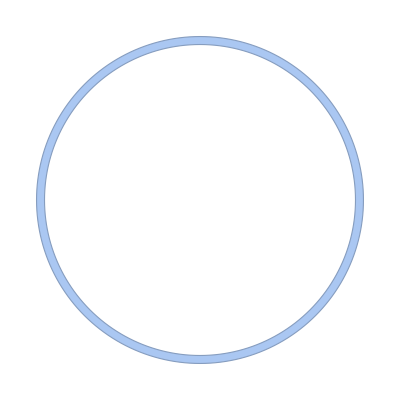

```mathematica
thinRing = GetThinM87RingInUnitsOfM9[21.7,0.05,M9/.paramsGR]
```

#### get data

Obtain the lensing band data via free-floating bisection.

inner lensing band bisection in progress ...

... for 78.026 sec.

outer lensing band bisection in progress ...

... for 139.871 sec.

minimization in progress ...

... for 324.584 sec.

542.507

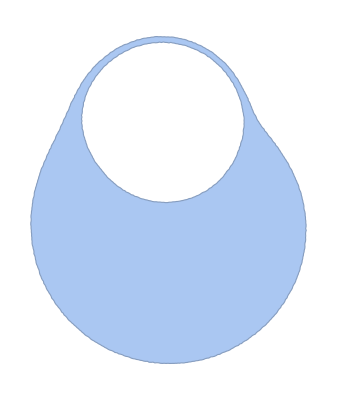
{0.696606,{x→-2.09158,y→4.36337},-Graphics-}

```mathematica
First@Timing[
	{minValue,minRule,LBregion} = GetMinimizedOverlap[
		camera/.paramsGR,
		paramsGR,
		thinRing, 
		HorizonCondition -> (($r < M + Sqrt[M^2 - α^2] + δHor)/.paramsGR),
		InitialBisectionPrecision->1*10^-3,
		MaxBisectionPrecision->5*10^-2,
		WhichLensingBandNumber->1,
		MinStepSize->Automatic,
		ShowProgressPlot->True,
		OutOfBoundsValue->100,
		MaxNumberOfSteps->∞,
		PlotRange->{{-#,#},{-#,#}}&@10
	];
]
LBdata[paramsGR]={minValue,minRule,LBregion}
```

#### plot for dynamic visualization in notebook

You may now look at the result of the lensing-band bisection and of the minimization.

```mathematica
area->minValue
paramsGR//N//TableForm

OverlayLensingBandsByHand[
	thinRing,LBregion,
	ScaleRange->{0.5,2},
	InitsXYS->Join[minRule[[All,2]],{1}],
	PlotRange->{{-10,10},{-10,10}},
	ImageSize->600
]
```

area→0.696606

G0→1.
incl→1.211
M9→7.82428
M→1.
α→0.611655
δHor→0.01

#### update minimization to also rescale (and plot for dynamic visualization in notebook)

We can also repeat the implemented minimization but now admit for rescaling. The latter amounts to choosing an asymptotic mass for which the minimization is optimal.
(Since we want to constrain the centroid shift by the diameter of the observed/assumed lensed emission region, we first need to obtain the latter. Herein, we assume that the latter is geometrically circular.)

```mathematica
diameterOfLBexp = (Max[#]-Min[#])&@(MeshCoordinates[thinRing][[All,1]])

Timing[{minValueUpdated,minRuleUpdated} = NMinimize[
	{AreaOfDifference[thinRing, LBregion, {x,y,s}]/Area[thinRing], x^2+y^2≤(diameterOfLBexp/2)^2,1/2<s<2},
	{x,y,s},
	Method->"RandomSearch"
]]
minValueUpdated = 1 - minValueUpdated
```

9.67756

{182.019,{0.,{x→1.19234,y→-0.0976691,s→0.911728}}}

1.

Once more, we can look at (and alter) the result of the minimization.

```mathematica
OverlayLensingBandsByHand[
	thinRing,LBregion,
	ScaleRange->{0.5,2},
	InitsXYS->minRuleUpdated[[All,2]],
	PlotRange->{{-10,10},{-10,10}},
	ImageSize->600
]
```

#### export visualization (before and after rescaling)

We prepare the shifted and rescaled observed/assumed emission region for visualization.

```mathematica
thinRingShifted = ShiftedAndRescaledRegion[thinRing,Evaluate[{-x,-y,1}/.minRule]];
```

```mathematica
thinRingShiftedAndRescaled = ShiftedAndRescaledRegion[thinRing,Evaluate[{-x*s,-y*s,1/s}/.minRuleUpdated]];
```

We also create a unique time stamp string to not overwrite previous results

```mathematica
timeStampString = ToString[AccountingForm[Round[AbsoluteTime[]]]];
```

Here is an example of how to plot and export results (before and after rescaling).

```mathematica
range = 11;
colLBtheory = Lighter@Lighter@Gray(*Opacity[0.4,Black]*);
colLBexperiment = Opacity[0.2,Yellow];

Show[
	(*frame*)
	GetPlotFrameLeft[{{-range,range},{-range,range}}],
	(*LB*)
	Graphics[{colLBtheory,BoundaryDiscretizeRegion@LBregion}],
	(*ring*)
	Graphics[{
			RGBColor["#1b9e77"],
			RegionIntersection[
				BoundaryDiscretizeRegion@thinRingShifted,
				BoundaryDiscretizeRegion@LBregion
			]
		}],
	Graphics[{
			RGBColor["#d95f02"],
			RegionDifference[
				BoundaryDiscretizeRegion@thinRingShifted,
				BoundaryDiscretizeRegion@LBregion
			]
		}],	
	Epilog->{
			Inset[Rotate[MaTeX["i="<>ToString[AccountingForm[N[incl*180/π/.paramsGR,2],NumberSigns->{"-", ""}]]],0],{-range,range}*0.9,{Left,Top}],
			Inset[Rotate[MaTeX["A="<>ToString[AccountingForm[N[s/.paramsGR,2],NumberSigns->{"-", ""}]]],0],{range,range}*0.9,{Right,Top}],
			Inset[Rotate[MaTeX["\\longrightarrow x"],0],{-range,-range}*0.95,{Left,Bottom}],
			Inset[Rotate[MaTeX["\\longrightarrow \\rotatebox[origin=c]{-90}{y}"],π/2],{-range,-range}*0.95,{Left,Bottom}]
		}
]

SetDirectory[NotebookDirectory[]];
Export["plots/randomCaseGR_"<>timeStampString<>"_beforeRescaling.pdf",%%]
```

-Graphics-

plots/randomCaseGR_3907749201_beforeRescaling.pdf

```mathematica
range = 11;
colLBtheory = Lighter@Lighter@Gray(*Opacity[0.4,Black]*);
colLBexperiment = Opacity[0.2,Yellow];

Show[
	(*frame*)
	GetPlotFrameLeft[{{-range,range},{-range,range}}],
	(*LB*)
	Graphics[{colLBtheory,BoundaryDiscretizeRegion@LBregion}],
	(*ring*)
	Graphics[{
			RGBColor["#1b9e77"],
			RegionIntersection[
				BoundaryDiscretizeRegion@thinRingShiftedAndRescaled,
				BoundaryDiscretizeRegion@LBregion
			]
		}],
	Graphics[{
			RGBColor["#d95f02"],
			RegionDifference[
				BoundaryDiscretizeRegion@thinRingShiftedAndRescaled,
				BoundaryDiscretizeRegion@LBregion
			]
		}],	
	Epilog->{
			Inset[Rotate[MaTeX["i="<>ToString[AccountingForm[N[incl*180/π/.paramsGR,2],NumberSigns->{"-", ""}]]],0],{-range,range}*0.9,{Left,Top}],
			Inset[Rotate[MaTeX["A="<>ToString[AccountingForm[N[s/.paramsGR,2],NumberSigns->{"-", ""}]]],0],{range,range}*0.9,{Right,Top}],
			Inset[Rotate[MaTeX["\\longrightarrow x"],0],{-range,-range}*0.95,{Left,Bottom}],
			Inset[Rotate[MaTeX["\\longrightarrow \\rotatebox[origin=c]{-90}{y}"],π/2],{-range,-range}*0.95,{Left,Bottom}]
		}
]

SetDirectory[NotebookDirectory[]];
Export["plots/randomCaseGR_"<>timeStampString<>"_afterRescaling.pdf",%%]
```

-Graphics-

plots/randomCaseGR_3907749201_afterRescaling.pdf

Finally, we also save the respective parameter choice.

```mathematica
SetDirectory[NotebookDirectory[]];
Export["plots/randomCaseBeyondGR_"<>timeStampString<>"_params.dat",paramsGR]
```

plots/randomCaseBeyondGR_3907749201_params.dat